# Solar wind discontinuities and ion scattering

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
PacletDirectoryLoad["~/src/Beforerr.m"];
<<Beforerr`;
<<utilities.wl
<<m/rules.wl
```

```mathematica
SetDirectory@NotebookDirectory[];
SetOptions[safeSave,"dir"->"../figures/",fmts->{".svg",".pdf"}];
(*SetOptions[ParametricPlot3D,AxesStyle->Large];*)
(*SetOptions[$FrontEndSession,GraphicsBoxOptions->{AxesStyle->{}}]*)
```

```mathematica
On[Assert];
notationRules=Join[
{B0->Subscript[B, 0],α->θ,Bz->Subscript[B, z],B0in->Subscript[B, t]},
{f1->Subscript[f, 1][z],f2->Subscript[f, 2][z],Cβ->Subscript[C, β]},
{xN->x̃,zN->z̃,Lref->Subscript[L, ref]},
{pxN->OverTilde[Subscript[p, x]],pzN->OverTilde[Subscript[p, z]]},
{px->Subscript[p, x],py->Subscript[p, y],pz->Subscript[p, z]}
];
formRules=notationRules;
assums={c>0,q>0,L>0,B0>0,B0in>0};
```

## Introduction

## Theoretical Analysis

## Deduction

```mathematica
BRules={
Bx[z_]:> B0in Sin[β Tanh[z/L]],
By[z_]:> B0in Cos[β Tanh[z/L]],
B0in->B0 Sin[θ],Bz->B0 Cos[θ]
};
B2Rules={Bx[z_]:> B0in Tanh[z/L],By[z_]:> CBy};
B3Rules={Bx[z_]:> B0in z/L,By[z_]:> B0in √(1-(z/L)^2)};
B3AntonRules={Bx[z_]:> B0in z/L,By[z_]:> B0in(1-z^2/(2 L^2))};
```

```mathematica
Ax:=Integrate[By[z],z]
Ay:=Integrate[-Bx[z],z]+ Integrate[Bz,x]
Az:=0
```

```mathematica
vecA:= {Ax,Ay,Az}
vecP={px,py,pz};
vecV:=vecP-(q vecA)/c;
Assert[(vecA{x,y,z})=={Bx[z],By[z],Bz}]
```

```mathematica
RHS:=1/(2m)vecV.vecV + q V/.{V->0}
rawEq:=rawH ==RHS
rawEq
```

rawH==(pz^2+(py-(q (Bz x-∫Bx[z]ⅆz))/c)^2+(px-(q ∫By[z]ⅆz)/c)^2)/(2 m)

```mathematica
fRules={f1->Integrate[By[z],z]/(B0in  L) ,f2->Integrate[-Bx[z],z]/(B0in  L) };
Ax:= f1 B0in L
Ay:= f2 B0in L  + Integrate[Bz,x]
```

#### Notations

```mathematica
{Subscript[A, x]->Ax,Subscript[A, y]->Ay}//.notationRules
Collect[{Subscript[f, 1]->f1,Subscript[f, 2]->f2}//.Join[fRules,BRules],{Cos[β],Sin[β]} ]
```

{A_x→L B_t f_1[z],A_y→x B_z+L B_t f_2[z]}

{f_1→1/2 Cos[β] (-CosIntegral[β-β Tanh[z/L]]+CosIntegral[β+β Tanh[z/L]])+1/2 Sin[β] (-SinIntegral[β-β Tanh[z/L]]+SinIntegral[β+β Tanh[z/L]]),f_2→1/2 (CosIntegral[β-β Tanh[z/L]]+CosIntegral[β+β Tanh[z/L]]) Sin[β]+1/2 Cos[β] (-SinIntegral[β-β Tanh[z/L]]-SinIntegral[β+β Tanh[z/L]])}

## Normalization

Normalize p=p̃ p, r =r̃ l with l=L
So H=H̃ h

```mathematica
normRules:=Join[
(*{Bref->B0,Lref->L,B0in->B0inN Bref},*)
{Bref->B0in},
{Lref->L,x->Lref xN + cxN1 ,cxN1->(c py)/(q Bz),z->zN Lref},
{p->(Bref q Lref)/c,px->pxN p,py->pyN p,pz->pzN p,m->(Bref^2 q^2 Lref^2)/(c^2 h)}];
```

```mathematica
HBar:=1/2  ( pzN^2+(pxN-f1 B0in/Bref)^2+(xN Bz/Bref+f2 B0in/Bref)^2)
Assert[Simplify[( h HBar-RHS)//.normRules]==0,assums]
```

```mathematica
normRules/.notationRules
h->(Bref^2 q^2 Lref^2)/(c^2 m)/.notationRules
"H̃"->HBar//.Join[BRules,normRules]/.notationRules
```

{Bref→B_t,L_ref→L,x→cxN1+x̃ L_ref,cxN1→(c p_y)/(q B_z),z→z̃ L_ref,p→(Bref q L_ref)/c,p_x→p OverTilde[p_x],p_y→p pyN,p_z→p OverTilde[p_z],m→(Bref^2 q^2 L_ref^2)/(c^2 h)}

h→(Bref^2 q^2 L_ref^2)/(c^2 m)

H̃→1/2 (OverTilde[p_z]^2+(OverTilde[p_x]-f_1[z])^2+(Cot[θ] x̃+f_2[z])^2)

### Asymptotic Hamiltonian near z=0

```mathematica
applyRules[x_,BRules_]:=Simplify[x//.Join[fRules,BRules]//.normRules]
fasym[f_,N_,BRules_]:={ff=applyRules[f,BRules]; f->Simplify[Series[ff,{zN,0,N}],assums],ff}
fasymB[BRules_,N_:3]:=Join[{BRules},{fasym[f1,#,BRules],fasym[f2,#,BRules]}/.notationRules& @N]
fasymB[BRules]
fasymB[B2Rules]
fasymB[B3Rules]
fasymB[B3AntonRules]
```

{{Bx[z_]:>B0in Sin[β Tanh[z/L]],By[z_]:>B0in Cos[β Tanh[z/L]],B0in→B0 Sin[θ],Bz→B0 Cos[θ]},{f_1[z]→z̃-1/6 β^2 (z̃)^3+O[z̃]^4,1/2 (-Cos[β] CosIntegral[β-β Tanh[z̃]]+Cos[β] CosIntegral[β+β Tanh[z̃]]+Sin[β] (-SinIntegral[β-β Tanh[z̃]]+SinIntegral[β+β Tanh[z̃]]))},{f_2[z]→(CosIntegral[β] Sin[β]-Cos[β] SinIntegral[β])-(β (z̃)^2)/2+O[z̃]^4,1/2 (CosIntegral[β-β Tanh[z̃]] Sin[β]+CosIntegral[β+β Tanh[z̃]] Sin[β]-Cos[β] (SinIntegral[β-β Tanh[z̃]]+SinIntegral[β+β Tanh[z̃]]))}}

{{Bx[z_]:>B0in Tanh[z/L],By[z_]:>CBy},{f_1[z]→(CBy z̃)/B_t+O[z̃]^4,(CBy z̃)/B_t},{f_2[z]→-(z̃)^2/2+O[z̃]^4,-Log[Cosh[z̃]]}}

{{Bx[z_]:>(B0in z)/L,By[z_]:>B0in √(1-(z/L)^2)},{f_1[z]→z̃-(z̃)^3/6+O[z̃]^4,1/2 (ArcSin[z̃]+z̃ √(1-(z̃)^2))},{f_2[z]→-(z̃)^2/2+O[z̃]^4,-(z̃)^2/2}}

{{Bx[z_]:>(B0in z)/L,By[z_]:>B0in (1-z^2/(2 L^2))},{f_1[z]→z̃-(z̃)^3/6+O[z̃]^4,z̃-(z̃)^3/6},{f_2[z]→-(z̃)^2/2+O[z̃]^4,-(z̃)^2/2}}

```mathematica
asyPlot[f_,n_:4,βTemp_:1]:=Block[{β=βTemp},
asyfs=Table[Asymptotic[f,{zN,0,i}],{i,n}];
Plot[{f,asyfs}//Evaluate,{zN,0,2},PlotLegends->"Expressions"]
]
```

## Equations

We introduce the potential energy U(κ x,p_x,z) = H − 1/2 p_z^2 of particle motion in the phase plane (z, p_z) of fast variables
At the saddle point (z=z_c, p_z=0) of the separatrix, the potential energy U has a local maximum value; thus, ∂U/∂z = 0. We use this condition to express slow coordinates along the uncertainty curve in the plane (κ x, p_x) as functions of z_c .

```mathematica
asymFRules[BRules_]:={Normal@fasym[f1,3,BRules][[1]],Normal@fasym[f2,3,BRules][[1]]}
asymFRules[BRules]
```

{f1→zN-(zN^3 β^2)/6,f2→-(zN^2 β)/2+CosIntegral[β] Sin[β]-Cos[β] SinIntegral[β]}

```mathematica
ClearAll[rulesF]
rulesF[BRules_:BRules,asym_:False]:=Module[{},
If[asym,
asymFRules[BRules],
(fRules//.BRules)//.normRules
]~Join~Join[BRules,normRules,{xN->κxN/Cot[θ]}]
]
HU[BRules_List:BRules,asym_Boole:False]:=Simplify[{HBar,U}//.rulesF[BRules,asym]]
```

```mathematica
U:=Simplify[HBar-1/2 pzN^2]
asymRules=rulesF[BRules,True];
exactRules=rulesF[BRules,False];
{Hasym,Uasym}=Simplify[{HBar,U}//.asymRules];
{Hexact,Uexact}=Simplify[{HBar,U}//.exactRules];
{Uasym,Uexact}/.notationRules
```

{1/2 ((-z̃+1/6 β^2 (z̃)^3+OverTilde[p_x])^2+(κxN-(β (z̃)^2)/2+CosIntegral[β] Sin[β]-Cos[β] SinIntegral[β])^2),1/8 ((2 κxN+CosIntegral[β-β Tanh[z̃]] Sin[β]+CosIntegral[β+β Tanh[z̃]] Sin[β]-Cos[β] SinIntegral[β-β Tanh[z̃]]-Cos[β] SinIntegral[β+β Tanh[z̃]])^2+(Cos[β] CosIntegral[β-β Tanh[z̃]]-Cos[β] CosIntegral[β+β Tanh[z̃]]+2 OverTilde[p_x]+Sin[β] SinIntegral[β-β Tanh[z̃]]-Sin[β] SinIntegral[β+β Tanh[z̃]])^2)}

```mathematica
eq[H_,U_]:={D[U,zN]==0,H==erg/.{pzN->0}}
eq[{H_,U_}]:=eq[H,U]
eqBRule[BRules_,asym_]:=eq[HU[BRules,asym]]

uncertaintyCurveEqs[H_,U_]:=eq[H,U]~Join~{D[U,{zN,2}]<0}

sol:=SolveValues[
eq,{κxN,pxN},Reals
];
uncertaintyCurveSolD:=SolveValues[
uncertaintyCurveEqs[Hasym,Uasym],{κxN,pxN},Reals
]
(*uncertaintyCurveSolD is not working in 14.1?*)
```

```mathematica
plotLabel="Uncertainty curve";
axesLabel={HoldForm[κ x],HoldForm[Subscript[p, x]]};

uCurveEqsExact[βi_:1,ergi_:1/2]:=Block[{β=Rationalize[βi],erg=Rationalize[ergi]},
uncertaintyCurveEqs[Hexact,Uexact]
]

uCurveEqsAsym[βi_:1,ergi_:1/2]:=Block[{β=Rationalize[βi],erg=Rationalize[ergi]},
uncertaintyCurveEqs[Hasym,Uasym]
]

solveEq[eq_,zNi_:1]:=NSolveValues[N[eq/.{zN->zNi}],{κxN,pxN},Reals]

uncertaintyCurvePlotExact[βi_:1,ergi_:1/2,zmax_:3]:=Module[{tempEq},
tempEq=uCurveEqsExact[βi,ergi];
ParametricPlot[
solveEq[tempEq,zNi],{zNi,-zmax,zmax},
AxesLabel->axesLabel,PlotLabel->plotLabel
]
]

uncertaintyCurvePlotAsym[βi_:1,ergi_:1/2,zmax_:3]:=Block[{tempSol,β=Rationalize[βi],erg=Rationalize[ergi]},
tempSol=N[uncertaintyCurveSolD];
ParametricPlot[tempSol,{zN,-zmax,zmax},
AxesLabel->axesLabel,PlotLabel->plotLabel
]
]

uncertaintyCurvePlots[βi_:1,ergi_:1/2,zmax_:3]:={
uncertaintyCurvePlotExact[βi,ergi,zmax],
uncertaintyCurvePlotAsym[βi,ergi,zmax]
}
```

### Plot

```mathematica
Manipulate[
uncertaintyCurvePlots[βi,ergi,zmax],
{{βi,1},0,3,Appearance->"Labeled"},
{{ergi,1/2},1/10,100,Appearance->"Labeled"},
{{zmax,3},1,5}
]
```

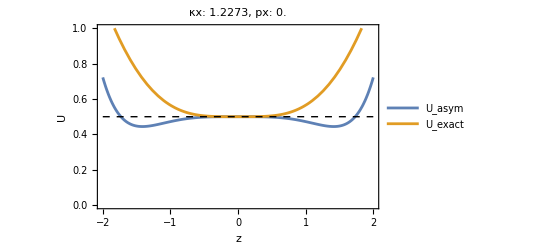

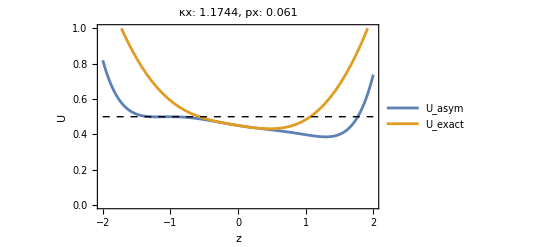

```mathematica
U2plot={Uasym,Uexact}/.{β->1};
plotLegends=Placed[{"U_asym","U_exact"},{Center,Top}];
uNPlot[U2plot,1.2273,0,2,1/2,PlotLegends->plotLegends]
uNPlot[U2plot,1.1744,0.061,2,1/2,PlotLegends->plotLegends]
```

"erg>1/β^2" is the condition for Uncertainty curve

## Length of uncertainty curve

```mathematica
solPlot[βi_:1,ergi_:1/2,zmax_:3]:=Block[{tsol,β=Rationalize[βi],erg=Rationalize[ergi]},
tsol=N[sol];
ParametricPlot[tsol,{zN,-zmax,zmax},AxesLabel->{HoldForm[κ x],HoldForm[Subscript[p, x]]}]
]
solLength[sol_]:=Module[{},
If[Length[sol[[1]]]>=2,
range = sol[[1]][[2]];
ArcLength[N@sol,{range[[3]],First@range,Last@range}],
0
]
]
solsLength[sols_]:=Total[solLength/@sols]

(*Discretized*)
eqLengthD[eq_,zmax_:3,i_:100]:=Module[{ps},
ps=ParallelTable[solveEq[eq,zN],{zN,-zmax,zmax,zmax/i}];
ps=First/@Select[ps,Length[#]>0&];
If[Length@ps>2,ArcLength[Line[ps]],0]
]

uCurveLengthD[f_:uCurveEqsExact,βi_:1,ergi_:1/2,zmax_:3,i_:100]:=eqLengthD[f[βi,ergi],zmax,i]


ucFrameLabel={"β","H"};
ucPlotLabel="Length of uncertainty curve";
ucNormPlotLabel="Length of normalized uncertainty curve";
uncertaintyCurveLengthScan:=(
tempsol=uncertaintyCurveSolD;
DensityPlot[
solsLength[tempsol//.{β->x,erg->y}],{x,0,3},{y,1/10,100},
ScalingFunctions->{None,"Log"},
FrameLabel->ucFrameLabel,PlotLegends->Automatic
]
)
```

#### Assuming L∝ β^α, for specific energy, check how does the length of uncertainty curve scales with β.

```mathematica
ClearAll[uncertaintyCurveLengthScanScaling]
uncertaintyCurveLengthScanScaling[f_:uCurveEqsExact,α_:1,erg0_:1,zmax_:3,i_:100]:=
Plot[
eqLengthD[f[β,(erg0/β^(2 α))],zmax,i]/√(erg0/β^(2 α)),{β,1/10,2},
AxesLabel->{"β",ucNormPlotLabel},
PlotLegends->Automatic,PlotRange->Full,MaxRecursion->0
]
```

NSolveValues::nsmet: This system cannot be solved with the methods available to NSolveValues.

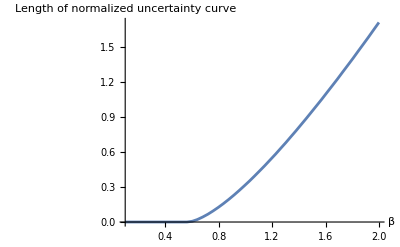

NSolveValues::nsmet: This system cannot be solved with the methods available to NSolveValues.

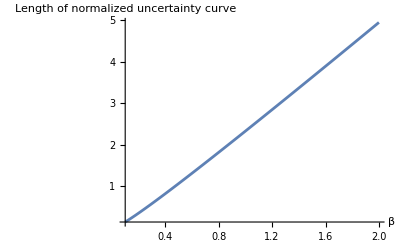

```mathematica
uncertaintyCurveLengthScanScaling[uCurveEqsExact,0.38]
uncertaintyCurveLengthScanScaling[uCurveEqsExact,0.38,100]
```

NSolveValues::nsmet: This system cannot be solved with the methods available to NSolveValues.

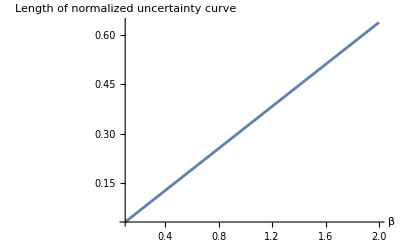

```mathematica
uncertaintyCurveLengthScanScaling[uCurveEqsExact,1]
```

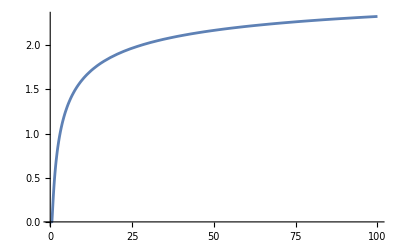

```mathematica
uncertaintyCurveLengthScanP[f_:uCurveEqsAsym,zmax_:3,i_:100]:=
Plot[
eqLengthD[f[1,y],zmax,i]/√y,{y,1/10,100},
PlotLegends->Automatic,PlotRange->Full
]
uncertaintyCurveLengthScanP[uCurveEqsExact]
```

```mathematica
solsLength[uncertaintyCurveSolD//.{β->1,erg->3}]
eqLengthD[uCurveEqsAsym[1,3]]
eqLengthD[uCurveEqsExact[1,3]]
```

$Aborted

4.97654

1.73025

```mathematica
pβ=Plot[1/β^2,{β,0,3},ScalingFunctions->{None,"Log"}];
```

#### Scan across β and Energy

```mathematica
uncertaintyCurveLengthScanD[f_:uCurveEqsAsym,zmax_:3,i_:100]:=(
DensityPlot[
eqLengthD[f[x,y],zmax,i]/√y,{x,0,π/2},{y,1/10,100},
ScalingFunctions->{None,"Log"},
FrameLabel->ucFrameLabel,PlotLegends->BarLegend[Automatic,LegendLabel->"L_uc"]
]
)
p1=uncertaintyCurveLengthScanD[uCurveEqsExact]
```

NSolveValues::nsmet: This system cannot be solved with the methods available to NSolveValues.

```mathematica
safeSave["UCLength",Show[p1,LabelStyle->Larger]]
```

{../figures/UCLength.svg,../figures/UCLength.pdf}

Already exists: ../figures/zPz_phase_portraits.svg

Already exists: ../figures/zPz_phase_portraits.pdf

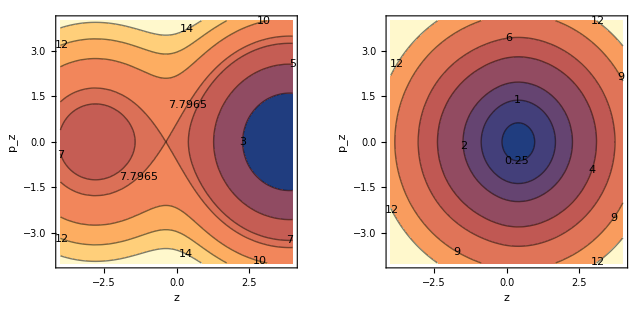

```mathematica
ClearAll[phasePortraits]

phasePortraits[H_,opts:OptionsPattern[]]:=ContourPlot[
Evaluate[H],{zN,-4,4},{pzN,-4,4},
FrameLabel->{"z","p_z"},
ContourLabels->True,BaseStyle->FontSize->18,
Evaluate[FilterRules[{opts},Options[ContourPlot]]]
]

pc1=phasePortraits[
Hexact/.{β->1,κxN->4,pxN->1},
Contours->{3,5,7,7.7965,10,12,14}
];

pc2=phasePortraits[
Hexact/.{β->1,κxN->0,pxN->1/2},
Contours->{0.25,1,2,4,6,9,12}
];

safeSave["zPz_phase_portraits",GraphicsRow[{pc1,pc2}]]
```

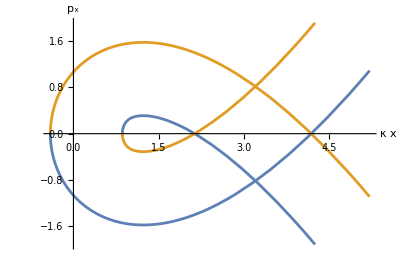
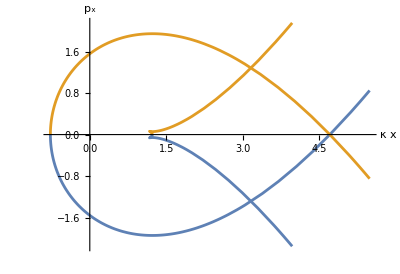
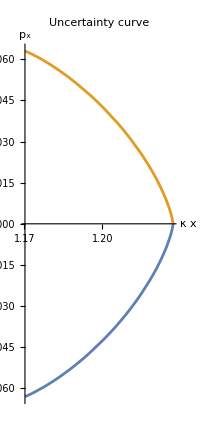
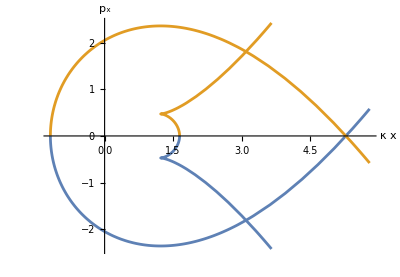
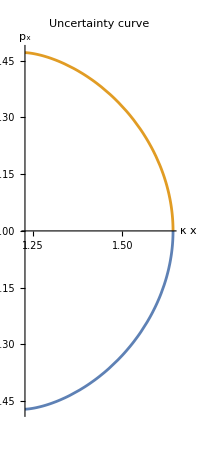
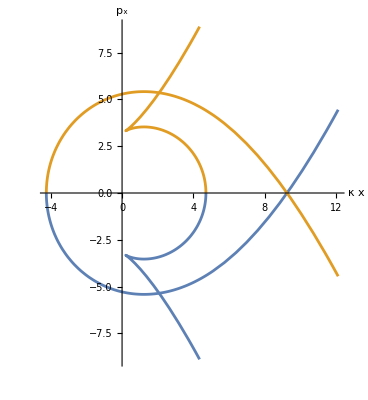
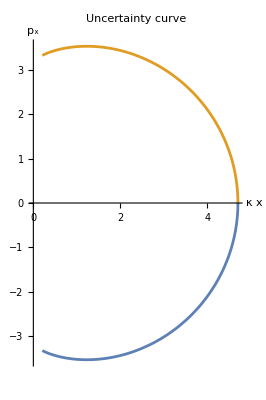
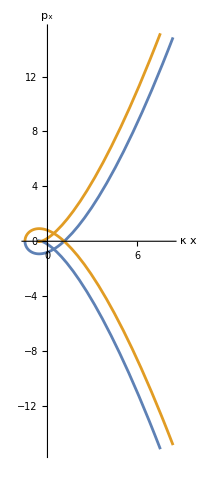
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
ApplyFs[fs_,expr_]:=Apply[#,expr]&/@fs
ApplyFs[{solPlot,uncertaintyCurvePlot},#]&/@{{1,1/5},{1,1/2},{1,1},{1,10,4},{2,1/10}}
```